```mathematica
<<"/Users/dave/Research/git/phd/graphs/support/PhDGraphSupport.m";
```

```mathematica
noTrace ={7.175351,6.846172,7.299156,7.116985,7.625429,7.083459,7.223481,7.097024,7.676731,6.913448,7.059351,6.830107,6.93988,7.129442,6.654909,6.886345,6.71428,6.847523,6.875458,6.649604,6.856021,6.718743,6.711655,6.834318,6.65582,6.736102,6.711877,6.734892,6.812803,6.615769,6.631172,6.640454,6.642732,6.880182,6.759315,6.702503,6.981536,6.617112,6.642031,6.875515,6.724085,6.65387,6.915434,6.863164,6.776737,6.736427,6.675027,6.732992,6.765677,6.81031,6.672298,6.688008,6.874559,6.694287,6.703374,7.052746,6.710716,6.932024,6.833717,6.679384,6.971478,6.734053,6.87469,7.022471,7.530441,6.997906,6.999299,7.159272,7.062324,7.292204,7.099835,7.303341,7.558945,7.203684,7.074734,7.389527,7.292137,8.767003,7.480804,6.922328,6.657073,6.620801,6.69952,6.704067,6.722984,6.66008,6.639434,6.693092,6.638491,6.638805,6.63993,6.727859,6.617922,6.720108,6.901364,7.749104,6.979544,7.123111,6.693982,6.831923};
```

```mathematica
traceThunk = {6.612257,6.781163,6.482326,6.49352,6.482708,6.484922,6.429779,6.519238,6.847352,6.459699,6.548022,6.589428,6.661861,6.441425,6.486637,6.532304,6.446402,6.345784,6.472227,6.421193,6.49033,6.430369,6.334737,6.422535,6.42896,6.587724,6.361909,6.542825,6.47086,6.497778,6.369187,6.397921,6.399315,6.710702,6.567432,6.905231,6.701894,6.777063,6.395269,6.385089,6.502203,6.391489,6.497291,6.504871,6.489605,6.326631,6.612632,7.033755,6.578134,6.432366,6.393286,6.456177,6.449749,6.41825,6.500414,6.399389,6.610466,6.908586,6.565676,6.4481,6.499449,6.900584,6.572572,6.760934,6.483302,6.541427,6.415503,6.580816,6.456385,6.548169,6.484024,6.392705,6.403852,6.432354,6.723232,6.782686,6.489987,6.590932,6.490125,6.586596,6.634534,6.445687,6.529397,6.57674,6.61712,6.42818,6.51552,6.999529,7.111078,7.767674,7.494391,7.591542,6.546796,6.439912,6.649153,6.52111,6.483193,6.583297,7.15931,6.437797};
```

```mathematica
traceSum={5.767638,5.756038,5.74945,5.785259,5.78347,5.80056,5.669069,5.767308,5.789125,5.737673,5.747458,5.746422,5.772974,5.798337,5.679464,5.727941,5.82236,5.761456,5.766067,5.753486,5.828617,5.793262,5.772122,5.699453,5.767894,5.875214,6.174411,6.358154,7.093513,6.167969,6.16392,6.212678,6.393937,6.617108,6.312051,6.300307,6.413046,6.342235,6.35581,6.271846,6.301265,6.239222,6.314296,6.287847,6.381099,6.271043,6.230607,6.238787,6.269455,6.19373,6.339841,6.438505,6.212375,6.273411,6.228002,6.28892,6.363822,6.440565,6.438549,6.342915,6.360447,6.355145,6.501202,6.445501,6.393048,6.35984,6.435325,6.531941,6.522965,6.385634,6.323774,6.562906,6.43404,6.409363,6.387369,6.540368,6.675797,6.382603,6.604685,6.370002,7.664932,6.555943,6.46895,6.351878,6.342911,6.588949,6.53506,6.321111,6.348706,6.334354,6.355,6.387103,6.42406,6.363369,6.330269,6.40374,6.419813,6.411018,6.453848,6.663787};
```

```mathematica
traceLinked = {5.618358,5.405171,5.484785,5.53723,5.528778,5.408106,5.540611,5.520023,5.592759,5.41393,5.526335,5.563877,5.583366,5.518052,5.416828,5.595744,5.602274,5.504192,5.414204,5.535162,5.617246,5.509472,5.399273,5.529249,5.496639,5.644864,5.444218,5.477314,5.946065,5.960619,5.607795,5.645632,5.468781,5.58023,5.537398,5.713066,5.643651,5.69835,5.794311,5.872306,5.903449,5.89849,5.887653,5.966415,5.967007,6.026768,5.908532,5.933498,5.968001,5.940701,5.907062,5.930429,5.888863,5.967229,5.903589,5.89498,6.029028,5.917685,5.883026,5.882801,5.932471,5.890805,5.792786,6.246237,5.761985,5.872845,5.998461,5.837975,5.930129,5.985298,5.944191,5.993278,5.96632,5.997286,5.938661,5.977722,5.875733,5.849048,6.041442,5.944569,5.914053,5.971636,6.055316,6.322266,5.96988,5.958411,6.083393,5.891851,5.975951,5.984112,5.938239,6.047231,6.007655,5.973856,6.061326,6.107874,6.723114,6.039645,6.074538,5.873929};
```

```mathematica
traceOptimized = {5.064992,4.825251,4.897588,4.8235,4.850225,4.87466,4.833295,4.991637,4.85349,4.94832,4.829287,4.959482,4.883042,4.909147,4.903946,4.838381,4.966463,4.850955,4.972728,4.847785,4.902152,4.855445,4.887009,5.043639,4.789682,4.97441,4.8585,4.913564,4.889845,4.963288,4.889252,4.795574,4.907832,4.859686,5.001539,4.850441,4.995565,4.882989,4.899781,4.863942,4.883051,4.826145,4.82883,4.886999,4.861746,4.902916,4.879483,4.918043,4.875708,4.917611,4.967539,4.818756,4.854582,4.855789,4.951213,4.869059,4.956977,4.847127,4.905589,4.892802,4.866952,4.972259,4.830107,4.980606,4.907885,5.019005,4.954023,5.128312,4.948567,5.05793,4.936634,4.995176,5.061992,5.238093,4.922975,5.127614,5.062632,5.07919,5.037775,4.983504,5.048037,4.968382,4.990441,5.044683,5.094788,4.957666,5.014888,5.077408,5.099535,4.92683,5.032835,5.035539,5.027425,4.934461,5.050547,4.932119,5.070252,5.069378,5.014014,5.037178};
```

```mathematica
ghcOptimized = {4.360961,4.366306,4.321351,4.386463,4.34129,4.383052,4.315967,4.296705,4.353676,4.344924,4.460554,4.334524,4.353512,4.324005,4.321552,4.320005,4.434314,4.396618,4.411715,4.352363,4.341493,4.457557,4.31937,4.325663,4.40516,4.381551,4.38731,4.503728,4.337566,4.33858,4.38715,4.385897,4.399708,4.317106,4.399431,4.318544,4.337183,4.512229,4.371038,4.346327,4.347739,4.338905,4.365322,4.405022,4.352996,4.314109,4.331369,4.422462,4.428109,4.343514,4.35193,4.383232,4.342832,4.367762,4.378011,4.312101,4.339605,4.34735,4.411902,4.531686,4.352599,4.311916,4.352592,4.355291,4.458231,4.372076,4.350206,4.36141,4.451988,4.408663,4.370449,4.324531,4.354571,4.360227,4.359433,4.366381,4.371407,4.36903,4.365385,4.33191,4.39908,4.368425,4.328248,4.399787,4.393669,4.40774,4.384548,4.377939,4.348646,4.381684,4.328128,4.45173,4.443676,4.672507,4.575767,4.421285,4.367923,4.402141,4.549814,4.456036};
```

```mathematica
cVersion = {0.194668,0.191452,0.222097,0.206966,0.187346,0.186594,0.186801,0.18768,0.187338,0.186594,0.187998,0.187253,0.211625,0.236563,0.187129,0.187689,0.186932,0.187175,0.188436,0.186608,0.186873,0.186274,0.189201,0.250496,0.191247,0.187598,0.188005,0.187957,0.186683,0.186928,0.186585,0.188264,0.186406,0.211895,0.206586,0.186885,0.186363,0.187183,0.18679,0.186812,0.186681,0.186643,0.187431,0.195839,0.231992,0.187662,0.187793,0.186507,0.186464,0.18696,0.187026,0.186902,0.186245,0.187807,0.223007,0.201191,0.188431,0.187314,0.188175,0.187498,0.188209,0.195647,0.190259,0.187296,0.21411,0.230176,0.186295,0.186155,0.186536,0.186714,0.186858,0.18614,0.197386,0.187043,0.20349,0.22785,0.18762,0.188861,0.187053,0.188001,0.18657,0.187665,0.186496,0.188551,0.186578,0.248201,0.199344,0.18794,0.187083,0.23274,0.188511,0.186449,0.188263,0.186245,0.186707,0.250218,0.203325,0.188657,0.188375,0.188837};
```

```mathematica
TableForm[
Table[
{x[[1]],
 Mean[x[[2]]],
 Median[x[[2]]], 
StandardDeviation[x[[2]]], 
SFRatio[ Median[noTrace], Median[x[[2]]]]
}, {x, 
{
{"", Times},
{NoTrace,noTrace },
{Thunk, traceThunk},
{Sum, traceSum},
{Linked, traceLinked},
{Optimized, traceOptimized},
{GhcOptimized, ghcOptimized},
{CVersion, cVersion}
}
}
]]
```

| Mean[Times] | Median[Times] | StandardDeviation[Times] | If[6.83282>Median[Times],6.83282/Median[Times]-1,1-Median[Times]/6.83282]
NoTrace | 6.91295 | 6.83282 | 0.323444 | 1.11022×10^-16
Thunk | 6.57902 | 6.49861 | 0.247435 | 0.0514274
Sum | 6.23896 | 6.3371 | 0.332858 | 0.0782255
Linked | 5.81253 | 5.89133 | 0.238623 | 0.15981
Optimized | 4.94186 | 4.9249 | 0.0889917 | 0.387402
GhcOptimized | 4.37975 | 4.36634 | 0.0604489 | 0.564884
CVersion | 0.19426 | 0.187641 | 0.0153046 | 35.4143

```mathematica
LocationTest[{noTrace, traceThunk},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 8847 | 5.53489×10^-21

```mathematica
LocationTest[{noTrace, traceSum},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 9785 | 1.42723×10^-31

```mathematica
LocationTest[{noTrace, traceLinked},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 9964 | 7.52798×10^-34

```mathematica
Needs["PlotLegends`"]
```

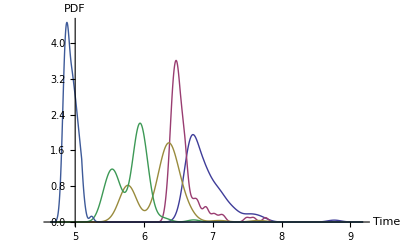

```mathematica
SmoothHistogram[{noTrace,traceThunk, traceSum, traceLinked, traceOptimized}, PlotStyle -> Thick,
AxesLabel -> {"Time", "PDF"}]
```